```mathematica
(*Note: This is not real data and used purely for practice*)
```

```mathematica
data={
{"A","North",250,50},
{"B","South",150,30},
{"C","East",200,40},
{"D","West",300,60},
{"E","North",270,55},
{"F","East",220,45},
{"G","South",180,35},
{"H","West",310,65}
};
keys= {"Product","Region","Sales","Profit"};
```

```mathematica
tab=Tabular[data,keys]
```

```mathematica
ColumnKeys[tab]
```

{Product,Region,Sales,Profit}

```mathematica
totalSales=Total[tab[[All,"Sales"]]]
totalProfit=Total[tab[[All,"Profit"]]]
```

1880

380

```mathematica
averageSalesByRegion=AggregateRows[tab,"averageSales"->Function[Mean[#Sales]],"Region"]
```

```mathematica
highProfitProducts=Select[tab,#Profit>50&]
```

```mathematica
sales=Normal[tab[[All,"Sales"]]];
products=Normal[tab[[All,"Product"]]];
```

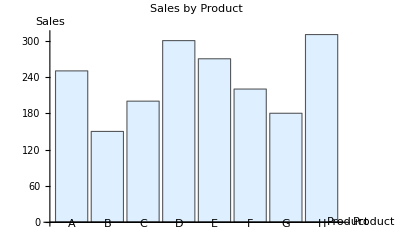

```mathematica
BarChart[tab->"Sales",ChartLabels->products,ChartStyle->LightBlue,AxesLabel->{"Product","Sales"},PlotLabel->"Sales by Product"]
```

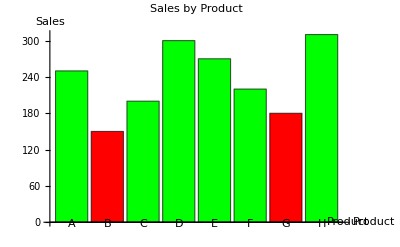

```mathematica
BarChart[
tab->"Sales",ChartLabels->products,ChartStyle->(If[#<200,Red,Green]&/@sales),
AxesLabel->{"Product","Sales"},PlotLabel->"Sales by Product"
]
```

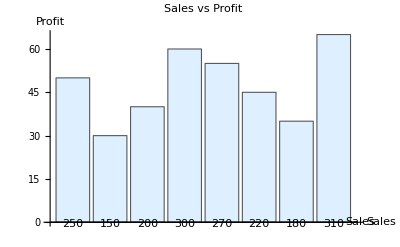

```mathematica
profit=Normal[tab[[All,"Profit"]]];
BarChart[tab->"Profit",ChartLabels->sales,ChartStyle->LightBlue,AxesLabel->{"Sales","Profit"},PlotLabel->"Sales vs Profit"]
```

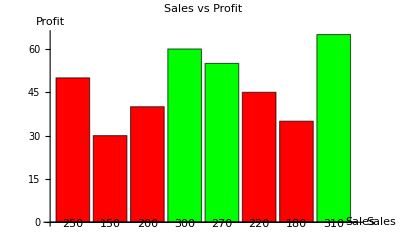

```mathematica
BarChart[tab->"Profit",ChartLabels->sales,ChartStyle->(If[#>50,Green,Red]&/@profit),AxesLabel->{"Sales","Profit"},PlotLabel->"Sales vs Profit"]
```

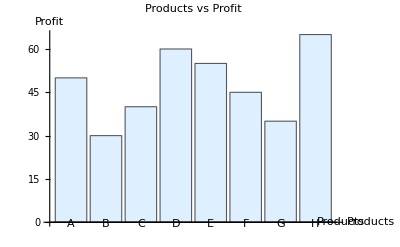

```mathematica
BarChart[tab->"Profit",ChartLabels->products,ChartStyle->LightBlue,AxesLabel->{"Products","Profit"},PlotLabel->"Products vs Profit"]
```

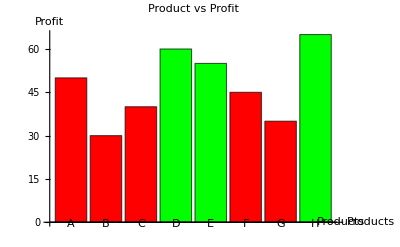

```mathematica
BarChart[tab->"Profit",ChartLabels->products,ChartStyle->(If[#>50,Green,Red]&/@profit),AxesLabel->{"Products","Profit"},PlotLabel->"Product vs Profit"]
```